```mathematica
SetDirectory[NotebookDirectory[]]
<<HQSimulation`
```

/home/ampolloreno/Downloads

Get::noopen: Cannot open PhysicsConstants`.

Needs::nocont: Context PhysicsConstants` was not created when Needs was evaluated.

```mathematica
SpinStates={2};
ModeCutoffs={};
GetOperators[SpinStates,ModeCutoffs,Display->True]
```

| Operator | Description
 | OpId | Identity operator
 | OpA | OpA[j] is the annihilation operator for mode j=1,2,3,...
 | OpAdag | OpAdag[j] is the creation operator for mode j=1,2,3,...
 | OpN | OpN[j] is the number operator for mode j=1,2,3,...
 | OpSwap | OpSwap[j,α=0,1,2,...,β=0,1,2,...] is the transition operator |β⟩⟨α| for ion j=1,2,3,...
 | Hilbert space dimension | HSdim=2

```mathematica
X=OpSwap[1,0,1]+OpSwap[1,1,0];
Y=ⅈ(OpSwap[1,0,1]-OpSwap[1,1,0]);
Z=-(OpSwap[1,1,1]-OpSwap[1,0,0]);
```

```mathematica
H[B_,ω_,t_]=B^2*t*X+B*Cos[ω t]Z;
vec0=Normalize[{1,1}]
```

{1/(√2),1/(√2)}

```mathematica
tmax=10;
SEQSolve[H[1,1,t],vec0,{0,tmax}];
SEQSolve[H[0,1,t],vec0,{0,tmax},FinalState->True]
```

{0.707107,0.707107}

```mathematica
ψ[B_?NumericQ,ω_?NumericQ,T_?NumericQ]:= SEQSolve[H[B,ω,t],vec0,{0,T},FinalState->True];
```

```mathematica
(*ϕ[B_?NumericQ,ω_?NumericQ,T_?NumericQ]:=Derivative[1, 0, 0][ψ][B, ω, T]*)
ϕ[B_?NumericQ,ω_?NumericQ,T_?NumericQ]:=Module[{eps = 0.000001},
vec1=SEQSolve[H[B,ω,t],vec0,{0,T},FinalState->True,PrecisionGoal->14,AccuracyGoal->14];
vec2=SEQSolve[H[B+eps,ω,t],vec0,{0,T},FinalState->True,PrecisionGoal->14,AccuracyGoal->14];
Return[(vec2-vec1)/eps];
]
```

```mathematica
ψ[1, 0, 1]
ϕ[1,0, 1]
QFI[B_?NumericQ,ω_?NumericQ,T_?NumericQ]:=4 (Norm[ϕ[B,ω,T]]^2+ (Conjugate[ϕ[B,ω,T]].ψ[B,ω,T])^2);
```

{0.414109-0.842763 ⅈ,0.208121+0.273771 ⅈ}

{-0.568992-0.62223 ⅈ,-1.11653-0.205989 ⅈ}

```mathematica
IQFI[B_?NumericQ, T_?NumericQ] :=NIntegrate[QFI[B, ω, T], {ω,1,10}]
IQFI[1, 1]
```

9.03095-0.0000311395 ⅈ

433139.

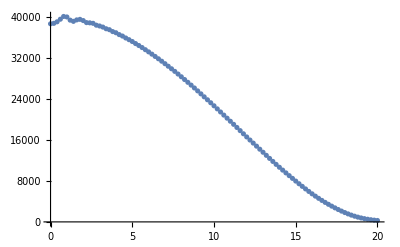

```mathematica
QFIlist=Table[{ω,QFI[1,ω,10]},{ω,0,20,0.2}];
Re[Total[QFIlist[[;;,2]]]0.2]
ListPlot[Re[QFIlist],PlotRange->All]
```

```mathematica
DiscretePlot[{{16.39428251055576, 211.81720109702593, 1267.863097098045}}]
```

DiscretePlot::argr: DiscretePlot called with 1 argument; 2 arguments are expected.

DiscretePlot[{{16.3943,211.817,1267.86}}]

```mathematica
Series[(Sin[ω*(t + δ)] - Sin[ω*t])/ω, {δ, 0, 3}]
```

Cos[t ω] δ-1/2 (ω Sin[t ω]) δ^2-1/6 (ω^2 Cos[t ω]) δ^3+O[δ]^4

```mathematica
Integrate[(Sin[ω*(Ti + δ)] - Sin[ω*(Ti)])/ω *(Sin[ω*(δ)])/ω , {ω, a, b}]
```

ConditionalExpression[-(-Cos[a Ti]+Cos[a (Ti-δ)]-Cos[a (Ti+δ)]+Cos[a (Ti+2 δ)]-a Ti SinIntegral[a Ti]+a (Ti-δ) SinIntegral[a (Ti-δ)]-a Ti SinIntegral[a (Ti+δ)]-a δ SinIntegral[a (Ti+δ)]+a Ti SinIntegral[a (Ti+2 δ)]+2 a δ SinIntegral[a (Ti+2 δ)])/(2 a)+(-Cos[b Ti]+Cos[b (Ti-δ)]-Cos[b (Ti+δ)]+Cos[b (Ti+2 δ)]-b Ti SinIntegral[b Ti]+b (Ti-δ) SinIntegral[b (Ti-δ)]-b Ti SinIntegral[b (Ti+δ)]-b δ SinIntegral[b (Ti+δ)]+b Ti SinIntegral[b (Ti+2 δ)]+2 b δ SinIntegral[b (Ti+2 δ)])/(2 b), ]

```mathematica
Integrate[(Sin[ω*(Ti + δ)] - Sin[ω*(Ti)])/ω *(Sin[ω*(δ)])/ω , ω]
```

1/2 (-Cos[Ti ω]/ω-Ti SinIntegral[Ti ω])+1/2 (Cos[(Ti-δ) ω]/ω+(Ti-δ) SinIntegral[(Ti-δ) ω])+1/2 (-Cos[(Ti+δ) ω]/ω-(Ti+δ) SinIntegral[(Ti+δ) ω])+1/2 (Cos[(Ti+2 δ) ω]/ω+(Ti+2 δ) SinIntegral[(Ti+2 δ) ω])

```mathematica
(-(-Cos[a Ti]+Cos[a (Ti-δ)]-Cos[a (Ti+δ)]+Cos[a (Ti+2 δ)]-a Ti SinIntegral[a Ti]+a (Ti-δ) SinIntegral[a (Ti-δ)]-a Ti SinIntegral[a (Ti+δ)]-a δ SinIntegral[a (Ti+δ)]+a Ti SinIntegral[a (Ti+2 δ)]+2 a δ SinIntegral[a (Ti+2 δ)])/(2 a)+(-Cos[b Ti]+Cos[b (Ti-δ)]-Cos[b (Ti+δ)]+Cos[b (Ti+2 δ)]-b Ti SinIntegral[b Ti]+b (Ti-δ) SinIntegral[b (Ti-δ)]-b Ti SinIntegral[b (Ti+δ)]-b δ SinIntegral[b (Ti+δ)]+b Ti SinIntegral[b (Ti+2 δ)]+2 b δ SinIntegral[b (Ti+2 δ)])/(2 b))/.δ->(T/n)/.Ti->(k*T/n)
```

-(-Cos[(a k T)/n]+Cos[a (-T/n+(k T)/n)]-Cos[a (T/n+(k T)/n)]+Cos[a ((2 T)/n+(k T)/n)]-(a k T SinIntegral[(a k T)/n])/n+a (-T/n+(k T)/n) SinIntegral[a (-T/n+(k T)/n)]-(a T SinIntegral[a (T/n+(k T)/n)])/n-(a k T SinIntegral[a (T/n+(k T)/n)])/n+(2 a T SinIntegral[a ((2 T)/n+(k T)/n)])/n+(a k T SinIntegral[a ((2 T)/n+(k T)/n)])/n)/(2 a)+(-Cos[(b k T)/n]+Cos[b (-T/n+(k T)/n)]-Cos[b (T/n+(k T)/n)]+Cos[b ((2 T)/n+(k T)/n)]-(b k T SinIntegral[(b k T)/n])/n+b (-T/n+(k T)/n) SinIntegral[b (-T/n+(k T)/n)]-(b T SinIntegral[b (T/n+(k T)/n)])/n-(b k T SinIntegral[b (T/n+(k T)/n)])/n+(2 b T SinIntegral[b ((2 T)/n+(k T)/n)])/n+(b k T SinIntegral[b ((2 T)/n+(k T)/n)])/n)/(2 b)

```mathematica
Series[-(-Cos[(a k T)/n]+Cos[a (-T/n+(k T)/n)]-Cos[a (T/n+(k T)/n)]+Cos[a ((2 T)/n+(k T)/n)]-(a k T SinIntegral[(a k T)/n])/n+a (-T/n+(k T)/n) SinIntegral[a (-T/n+(k T)/n)]-(a T SinIntegral[a (T/n+(k T)/n)])/n-(a k T SinIntegral[a (T/n+(k T)/n)])/n+(2 a T SinIntegral[a ((2 T)/n+(k T)/n)])/n+(a k T SinIntegral[a ((2 T)/n+(k T)/n)])/n)/(2 a), {a, ∞, 1}]//Normal
```

1/4 (-π √(((-1+k)^2 T^2)/n^2)+π √((k^2 T^2)/n^2)+π √(((1+k)^2 T^2)/n^2)-π √(((2+k)^2 T^2)/n^2))+Cos[(a (T+k T))/n]/(2 a)-Cos[(a (T+k T))/n]/(2 a (1+k))-(k Cos[(a (T+k T))/n])/(2 a (1+k))-Cos[(a (2 T+k T))/n]/(2 a)+Cos[(a (2 T+k T))/n]/(a (2+k))+(k Cos[(a (2 T+k T))/n])/(2 a (2+k))

```mathematica
1/(2 a)-1/(2 a (1+k))-k/(2 a (1+k))-1/(2 a)+1/(a (2+k))+k/(2 a (2+k))//FullSimplify
```

0